```mathematica
Ibias={3,3,5,5,2.5}
input1[t_]:=1Sin[π t/400]HeavisideTheta[t-00.1]
inputAnti[t_]:=1Sin[(π (t-400) /400)]HeavisideTheta[t-00.1]
inputAdv[t_]:=1Sin[(π (t-50) /400)]HeavisideTheta[t-00.1]
inputLag[t_]:=1Sin[(π (t+50) /400)]HeavisideTheta[t-00.1]


(*f1 = 3(*input corrisponding to 1*)
f2 = 3(*input corrisponding to 0*)
θ=40
input1[t_]:=f1 Iinj[100,300][t]+f1 Iinj[500,300][t]+f2 Iinj[900,300][t]
input2[t_]:=f1 Iinj[100+θ,300][t]+f2 Iinj[500+θ,300][t]+f1 Iinj[900+θ,300][t]
*)
time =1200
Fv[V_,W_][Ii_,k_,b_]:=-3V+((1/k)*V^2 +40+100b-W+Ii)
Fw[V_,W_][a_,b_]:=a (b(V)-W)
Iinj [start_,dur_][t_]:=HeavisidePi[(t-start)/dur-1/2]
T[x_]:=Transpose[x]
L[x_]:=Length[x]
(*base parameters of the neurons*)
k = 25
a =1/10.
b=1 (*rez*) (*.2 int*)
c= 20
d =.1
tau =10
Ii =-47
(*synaptic weights*)
go=4
gee = 2
gei = 8
gie = -10
gii = -10

ClassicalRungeKuttaCoefficients[4,prec_]:=With[{amat={{1/2},{0,1/2},{0,0,1}},bvec={1/6,1/3,1/3,1/6},cvec={1/2,1/2,1}},N[{amat,bvec,cvec},prec]]
```

{3,3,5,5,2.5}

1200

25

0.1

1

20

0.1

10

-47

4

2

8

-10

-10

```mathematica
Δt=2
Monitor[mydat=Reap[
Do[
q=i;qq=j;
isSolve=True;
Ibias={i,i,j,j,-2} ;
solSync=NDSolve[
{(*neuron e1*)
Ve1'[t]==Fv[Ve1[t],We1[t]][Ii,k,b]+input1[t]+gee Se2[t] +gie Si1[t]+Ibias[[1]],Ve1[0]==0,
We1'[t]==Fw[Ve1[t],We1[t]][a,b],We1[0]==6,
tau Se1'[t]== -Se1[t],Se1[0]==0,
WhenEvent[Ve1[t]==130,{Ve1[t]->c,We1[t]->We1[t]+d,Se1[t]->Se1[t]+1},"DetectionMethod"->"Sign","LocationMethod"->"LinearInterpolation"],
(*neuron e2*)
Ve2'[t]==Fv[Ve2[t],We2[t]][Ii,k,b]+input1[t]+gee Se1[t] +gie Si2[t]+Ibias[[2]],Ve2[0]==0,
We2'[t]==Fw[Ve2[t],We2[t]][a,b],We2[0]==6,
tau Se2'[t]== -Se2[t],Se2[0]==0,
WhenEvent[Ve2[t]==130,{Ve2[t]->c,We2[t]->We2[t]+d,Se2[t]->Se2[t]+1},"DetectionMethod"->"Sign","LocationMethod"->"LinearInterpolation"],
(*neuron i1*)
Vi1'[t]==Fv[Vi1[t],Wi1[t]][Ii,k,b]+input1[t]+gii Si2[t]+gei Se1[t]+Ibias[[3]],Vi1[0]==0,
Wi1'[t]==Fw[Vi1[t],Wi1[t]][a,b],Wi1[0]==6,
tau Si1'[t]== -Si1[t],Si1[0]==0,
WhenEvent[Vi1[t]==130,{Vi1[t]->c,Wi1[t]->Wi1[t]+d,Si1[t]->Si1[t]+1},"DetectionMethod"->"Sign","LocationMethod"->"LinearInterpolation"],
(*neuroni2*)
Vi2'[t]==Fv[Vi2[t],Wi2[t]][Ii,k,b]+input1[t]+gii Si1[t]+gei Se2[t]+Ibias[[4]],Vi2[0]==0,
Wi2'[t]==Fw[Vi2[t],Wi2[t]][a,b],Wi2[0]==6,
tau Si2'[t]== -Si2[t],Si2[0]==0,
WhenEvent[Vi2[t]==130,{Vi2[t]->c,Wi2[t]->Wi2[t]+d,Si2[t]->Si2[t]+1},"DetectionMethod"->"Sign","LocationMethod"->"LinearInterpolation"],
(*neuron out*)
Vo'[t]==Fv[Vo[t],Wo[t]][Ibias[[5]],k,.2]+go Se1[t]+go Se2[t],Vo[0]==0,
Wo'[t]==Fw[Vo[t],Wo[t]][a,.2],Wo[0]==6,
WhenEvent[Vo[t]==130,{Vo[t]->c,Wo[t]->Wo[t]+d},"DetectionMethod"->"Sign","LocationMethod"->"LinearInterpolation"]},
{Ve1,We1,Se1,Ve2,We2,Se2,Vi1,Wi1,Si1,Vi2,Wi2,Si2,Vo,Wo},{t,0,time},Method->{"TimeIntegration"->"Adams"},Compiled->True];

solAnti=NDSolve[
{(*neuron e1*)
Ve1'[t]==Fv[Ve1[t],We1[t]][Ii,k,b]+input1[t]+gee Se2[t] +gie Si1[t]+Ibias[[1]],Ve1[0]==0,
We1'[t]==Fw[Ve1[t],We1[t]][a,b],We1[0]==6,
tau Se1'[t]== -Se1[t],Se1[0]==0,
WhenEvent[Ve1[t]==130,{Ve1[t]->c,We1[t]->We1[t]+d,Se1[t]->Se1[t]+1},"DetectionMethod"->"Sign","LocationMethod"->"LinearInterpolation"],
(*neuron e2*)
Ve2'[t]==Fv[Ve2[t],We2[t]][Ii,k,b]+inputAnti[t]+gee Se1[t] +gie Si2[t]+Ibias[[2]],Ve2[0]==0,
We2'[t]==Fw[Ve2[t],We2[t]][a,b],We2[0]==6,
tau Se2'[t]== -Se2[t],Se2[0]==0,
WhenEvent[Ve2[t]==130,{Ve2[t]->c,We2[t]->We2[t]+d,Se2[t]->Se2[t]+1},"DetectionMethod"->"Sign","LocationMethod"->"LinearInterpolation"],
(*neuron i1*)
Vi1'[t]==Fv[Vi1[t],Wi1[t]][Ii,k,b]+input1[t]+gii Si2[t]+gei Se1[t]+Ibias[[3]],Vi1[0]==0,
Wi1'[t]==Fw[Vi1[t],Wi1[t]][a,b],Wi1[0]==6,
tau Si1'[t]== -Si1[t],Si1[0]==0,
WhenEvent[Vi1[t]==130,{Vi1[t]->c,Wi1[t]->Wi1[t]+d,Si1[t]->Si1[t]+1},"DetectionMethod"->"Sign","LocationMethod"->"LinearInterpolation"],
(*neuroni2*)
Vi2'[t]==Fv[Vi2[t],Wi2[t]][Ii,k,b]+inputAnti[t]+gii Si1[t]+gei Se2[t]+Ibias[[4]],Vi2[0]==0,
Wi2'[t]==Fw[Vi2[t],Wi2[t]][a,b],Wi2[0]==6,
tau Si2'[t]== -Si2[t],Si2[0]==0,
WhenEvent[Vi2[t]==130,{Vi2[t]->c,Wi2[t]->Wi2[t]+d,Si2[t]->Si2[t]+1},"DetectionMethod"->"Sign","LocationMethod"->"LinearInterpolation"],
(*neuron out*)
Vo'[t]==Fv[Vo[t],Wo[t]][Ibias[[5]],k,.2]+go Se1[t]+go Se2[t],Vo[0]==0,
Wo'[t]==Fw[Vo[t],Wo[t]][a,.2],Wo[0]==6,
WhenEvent[Vo[t]==130,{Vo[t]->c,Wo[t]->Wo[t]+d},"DetectionMethod"->"Sign","LocationMethod"->"LinearInterpolation"]},
{Ve1,We1,Se1,Ve2,We2,Se2,Vi1,Wi1,Si1,Vi2,Wi2,Si2,Vo,Wo},{t,0,time},Method->{"TimeIntegration"->"Adams"},Compiled->True];

solAdv=NDSolve[
{(*neuron e1*)
Ve1'[t]==Fv[Ve1[t],We1[t]][Ii,k,b]+input1[t]+gee Se2[t] +gie Si1[t]+Ibias[[1]],Ve1[0]==0,
We1'[t]==Fw[Ve1[t],We1[t]][a,b],We1[0]==6,
tau Se1'[t]== -Se1[t],Se1[0]==0,
WhenEvent[Ve1[t]==130,{Ve1[t]->c,We1[t]->We1[t]+d,Se1[t]->Se1[t]+1},"DetectionMethod"->"Sign","LocationMethod"->"LinearInterpolation"],
(*neuron e2*)
Ve2'[t]==Fv[Ve2[t],We2[t]][Ii,k,b]+inputAdv[t]+gee Se1[t] +gie Si2[t]+Ibias[[2]],Ve2[0]==0,
We2'[t]==Fw[Ve2[t],We2[t]][a,b],We2[0]==6,
tau Se2'[t]== -Se2[t],Se2[0]==0,
WhenEvent[Ve2[t]==130,{Ve2[t]->c,We2[t]->We2[t]+d,Se2[t]->Se2[t]+1},"DetectionMethod"->"Sign","LocationMethod"->"LinearInterpolation"],
(*neuron i1*)
Vi1'[t]==Fv[Vi1[t],Wi1[t]][Ii,k,b]+input1[t]+gii Si2[t]+gei Se1[t]+Ibias[[3]],Vi1[0]==0,
Wi1'[t]==Fw[Vi1[t],Wi1[t]][a,b],Wi1[0]==6,
tau Si1'[t]== -Si1[t],Si1[0]==0,
WhenEvent[Vi1[t]==130,{Vi1[t]->c,Wi1[t]->Wi1[t]+d,Si1[t]->Si1[t]+1},"DetectionMethod"->"Sign","LocationMethod"->"LinearInterpolation"],
(*neuroni2*)
Vi2'[t]==Fv[Vi2[t],Wi2[t]][Ii,k,b]+inputAdv[t]+gii Si1[t]+gei Se2[t]+Ibias[[4]],Vi2[0]==0,
Wi2'[t]==Fw[Vi2[t],Wi2[t]][a,b],Wi2[0]==6,
tau Si2'[t]== -Si2[t],Si2[0]==0,
WhenEvent[Vi2[t]==130,{Vi2[t]->c,Wi2[t]->Wi2[t]+d,Si2[t]->Si2[t]+1},"DetectionMethod"->"Sign","LocationMethod"->"LinearInterpolation"],
(*neuron out*)
Vo'[t]==Fv[Vo[t],Wo[t]][Ibias[[5]],k,.2]+go Se1[t]+go Se2[t],Vo[0]==0,
Wo'[t]==Fw[Vo[t],Wo[t]][a,.2],Wo[0]==6,
WhenEvent[Vo[t]==130,{Vo[t]->c,Wo[t]->Wo[t]+d},"DetectionMethod"->"Sign","LocationMethod"->"LinearInterpolation"]},
{Ve1,We1,Se1,Ve2,We2,Se2,Vi1,Wi1,Si1,Vi2,Wi2,Si2,Vo,Wo},{t,0,time},Method->{"TimeIntegration"->"Adams"},Compiled->True];

solLag=NDSolve[
{(*neuron e1*)
Ve1'[t]==Fv[Ve1[t],We1[t]][Ii,k,b]+input1[t]+gee Se2[t] +gie Si1[t]+Ibias[[1]],Ve1[0]==0,
We1'[t]==Fw[Ve1[t],We1[t]][a,b],We1[0]==6,
tau Se1'[t]== -Se1[t],Se1[0]==0,
WhenEvent[Ve1[t]==130,{Ve1[t]->c,We1[t]->We1[t]+d,Se1[t]->Se1[t]+1},"DetectionMethod"->"Sign","LocationMethod"->"LinearInterpolation"],
(*neuron e2*)
Ve2'[t]==Fv[Ve2[t],We2[t]][Ii,k,b]+inputLag[t]+gee Se1[t] +gie Si2[t]+Ibias[[2]],Ve2[0]==0,
We2'[t]==Fw[Ve2[t],We2[t]][a,b],We2[0]==6,
tau Se2'[t]== -Se2[t],Se2[0]==0,
WhenEvent[Ve2[t]==130,{Ve2[t]->c,We2[t]->We2[t]+d,Se2[t]->Se2[t]+1},"DetectionMethod"->"Sign","LocationMethod"->"LinearInterpolation"],
(*neuron i1*)
Vi1'[t]==Fv[Vi1[t],Wi1[t]][Ii,k,b]+input1[t]+gii Si2[t]+gei Se1[t]+Ibias[[3]],Vi1[0]==0,
Wi1'[t]==Fw[Vi1[t],Wi1[t]][a,b],Wi1[0]==6,
tau Si1'[t]== -Si1[t],Si1[0]==0,
WhenEvent[Vi1[t]==130,{Vi1[t]->c,Wi1[t]->Wi1[t]+d,Si1[t]->Si1[t]+1},"DetectionMethod"->"Sign","LocationMethod"->"LinearInterpolation"],
(*neuroni2*)
Vi2'[t]==Fv[Vi2[t],Wi2[t]][Ii,k,b]+inputLag[t]+gii Si1[t]+gei Se2[t]+Ibias[[4]],Vi2[0]==0,
Wi2'[t]==Fw[Vi2[t],Wi2[t]][a,b],Wi2[0]==6,
tau Si2'[t]== -Si2[t],Si2[0]==0,
WhenEvent[Vi2[t]==130,{Vi2[t]->c,Wi2[t]->Wi2[t]+d,Si2[t]->Si2[t]+1},"DetectionMethod"->"Sign","LocationMethod"->"LinearInterpolation"],
(*neuron out*)
Vo'[t]==Fv[Vo[t],Wo[t]][Ibias[[5]],k,.2]+go Se1[t]+go Se2[t],Vo[0]==0,
Wo'[t]==Fw[Vo[t],Wo[t]][a,.2],Wo[0]==6,
WhenEvent[Vo[t]==130,{Vo[t]->c,Wo[t]->Wo[t]+d},"DetectionMethod"->"Sign","LocationMethod"->"LinearInterpolation"]},
{Ve1,We1,Se1,Ve2,We2,Se2,Vi1,Wi1,Si1,Vi2,Wi2,Si2,Vo,Wo},{t,0,time},Method->{"TimeIntegration"->"Adams"},Compiled->True];

isSolve=False;
z=Sow[
Join[
Table[tt= t;Through[{Ve1,We1,Se1,Ve2,We2,Se2,Vi1,Wi1,Si1,Vi2,Wi2,Si2,Vo,Wo}[t]]/.solAnti[[1]],{t,0,time,Δt}],
Table[tt= t;Through[{Ve1,We1,Se1,Ve2,We2,Se2,Vi1,Wi1,Si1,Vi2,Wi2,Si2,Vo,Wo}[t]]/.solAdv[[1]],{t,0,time,Δt}],
Table[tt= t;Through[{Ve1,We1,Se1,Ve2,We2,Se2,Vi1,Wi1,Si1,Vi2,Wi2,Si2,Vo,Wo}[t]]/.solLag[[1]],{t,0,time,Δt}],
Table[tt= t;Through[{Ve1,We1,Se1,Ve2,We2,Se2,Vi1,Wi1,Si1,Vi2,Wi2,Si2,Vo,Wo}[t]]/.solSync[[1]],{t,0,time,Δt}]
]];
,{i,0,20,1},{j,0,20,1}]
][[2,1]];
,{q,qq,isSolve,tt}];
```

2

```mathematica
size=Sqrt[L[mydat]]
δ=40
isSpike[x_]:=Piecewise[{{3,200+δ<x[[1]]*Δt<time},{2,time+20+δ<x[[1]]*Δt<2*time},{1,2*time+20+δ<x[[1]]*Δt<3*time},{0,3*time+200+δ<x[[1]]*Δt<4*time},{-1,True}}]
hasSpiked=Table[
dat=FindPeaks[T[mydat[[size(kk-1)+jj]]][[-2]],0,0,60];
Table[isSpike[dat[[i]]],{i,1,L[dat]}],{kk,1,size},{jj,1,size}];
Dimensions[hasSpiked]
Logic=
{
{{0,0,0,0},"OFF"},
{{0,0,0,1},"AND"},
{{0,1,1,1},"OR"},
{{0,1,1,0},"XOR"},
{{1,1,1,0},"NAND"},
{{1,0,0,0},"NOR"},
{{1,0,0,1},"NXOR"},
{{1,1,1,1},"ON"},
{{0,1,0,0}, "NIMP1"},
{{0,0,1,0},"NIMP2"},
{{1,1,0,1},"IMP1"},
{{1,0,1,1},"IMP2"},
{{0,1,0,1},"AIMP1"},
{{0,0,1,1},"AIMP2"},
{{1,1,0,0},"XIMP1"},
{{1,0,1,0},"XIMP2"}
};
```

21

40

{21,21}

0.65

RGBColor[0.8, 0.1, 0.1]

RGBColor[0.9, 0.5, 0.2]

RGBColor[0.9, 0.8, 0.3]

RGBColor[0.1, 0.8, 0.4]

RGBColor[0.1, 0.4, 0.8]

RGBColor[0.7, 0.4, 0.8]

0.65

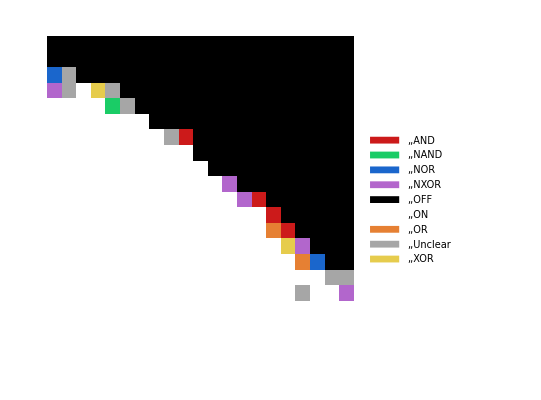

```mathematica
grey=.65
red = RGBColor[.8,.1,.1]
orange=  RGBColor[.9,.5,.2]
yellow=RGBColor[.9,.8,.3]
green= RGBColor[.1,.8,.4]
blue =RGBColor[.1,.4,.8]
purple=RGBColor[.7,.4,.8]

LabeledLogic=Table[
isTrue=Table[If[Count[hasSpiked[[kk,jj]],i]>1,1,0],{i,0,3}];
out=Logic[[Position[Logic,isTrue,Infinity][[1,1]],2]];
out,
{kk,1,size},{jj,1,size}];
MatLogic=Table[
isTrue=Table[If[Count[hasSpiked[[kk,jj]],i]>0,1,0],{i,0,3}];
out=Position[Logic,isTrue,Infinity][[1,1]],
{kk,1,size},{jj,1,size}];
grey=.65
outter =ArrayPlot[LabeledLogic,ColorRules->
{"OFF"->Black,"ON"->White,"AND"->red,"OR"->orange,"XOR"->yellow,"NAND"->green,"NOR"->blue,"NXOR"->purple,"Unclear"->GrayLevel[grey],"NIMP1"->GrayLevel[grey],"NIMP2"->GrayLevel[grey],"AIMP1"->GrayLevel[grey],"AIMP2"->GrayLevel[grey],"XIMP1"->GrayLevel[grey],"XIMP2"->GrayLevel[grey],"IMP1"->GrayLevel[grey],"IMP2"->GrayLevel[grey]},PlotLegends->Automatic,DataRange->{{2,6},{2,6}},FrameTicks->True]
(*thresholded to ignore transient spikes*)
```

```mathematica
Export["/home/ns-cclolab/Dropbox/Misc_Stuff, and Posters/LogicGates/outter
```